```mathematica
SetDirectory[NotebookDirectory[]];
```

# T_scaling

## data

```mathematica
fpi=Flatten[Import["./LPA_Tscaling_mub0/buffer/mSigma.dat"]];
T0=Flatten[Import["./LPA_Tscaling_mub0/buffer/TMeV.dat"]];
t=-(T0-T0[[1]])/T0[[1]];
datamub0=Transpose[{Log[-t[[2;;Length[t]]]],Log[1/fpi[[2;;Length[t]]]]}];
b1mub0=Transpose[{Log[-t[[2;;Length[t]-2]]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];
b1mub0linear=Transpose[{T0[[2;;Length[t]-2]],-Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T0]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub600/buffer/mSigma.dat"]];
T600=Flatten[Import["./LPA_Tscaling_mub600/buffer/TMeV.dat"]];
t=-(T600-T600[[1]])/T600[[1]];
datamub600=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub600=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub600[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T600]-2}]]}];

fpi=Flatten[Import["./LPA_Tscaling_mub641/buffer/mSigma.dat"]];
T641=Flatten[Import["./LPA_Tscaling_mub641/buffer/TMeV.dat"]];
t=-(T641-T641[[1]])/T641[[1]];
datamub641=Transpose[{Log[-t[[2;;Length[t]]]],Log[fpi[[2;;Length[t]]]]}];
b1mub641=Transpose[{Log[-t[[2;;Length[t]-2]]],Flatten[Table[FindFit[datamub641[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[T641]-2}]]}];
```

## Plot

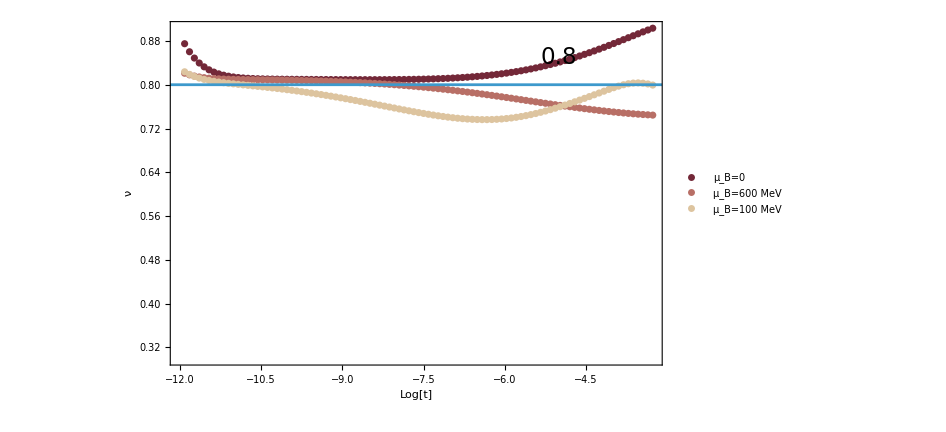

```mathematica
plotT=Show[ListPlot[{b1mub0,b1mub600,b1mub641},
Frame->True,FrameLabel->{Style["Log[t]",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.2}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0","μ_B=600 MeV","μ_B=100 MeV","μ_B=150 MeV","μ_B=200 MeV","μ_B=250 MeV","μ_B=300 MeV","μ_B=350 MeV","μ_B=400 MeV","μ_B=450 MeV","μ_B=500 MeV","μ_B=550 MeV","μ_B=600 MeV","μ_B=650 MeV","μ_B=700 MeV"},LabelStyle->16],{0.23,0.32}],
PlotRange->All(*{{-12,-2},{0.6,0.9}}*),AxesOrigin->{-12,0.3},FrameTicksStyle->Directive[15,Black]],
ListLinePlot[{{-13,0.8},{10,0.8}}],ImageSize->700,Background->None,Epilog->{Text[Style["0.8",23],{-5,0.85}]}]
```

```mathematica
Log[0.001/60.]
```

-11.0021